

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

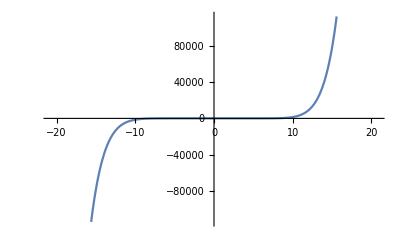

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-20.784609690826528,20.784609690826528}]
```

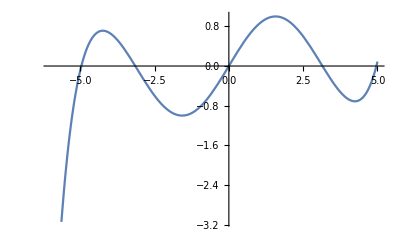

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-6,5}]
```

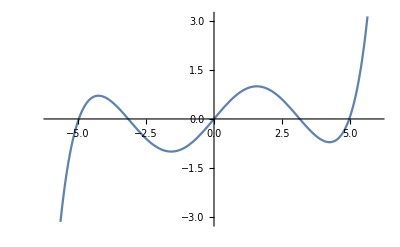

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-6,6}]
```

```mathematica
D[x-x^3/6+x^5/120-x^7/5040+x^9/362880,x]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

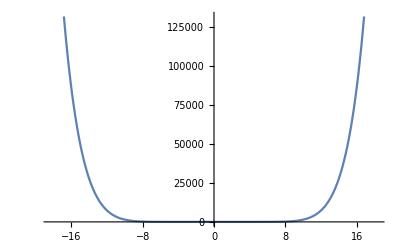

```mathematica
Plot[1-x^2/2+x^4/24-x^6/720+x^8/40320,{x,-18.33030277982336,18.33030277982336}]
```

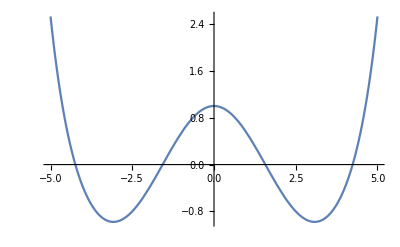

```mathematica
Plot[1-x^2/2+x^4/24-x^6/720+x^8/40320,{x,-5,5}]
```

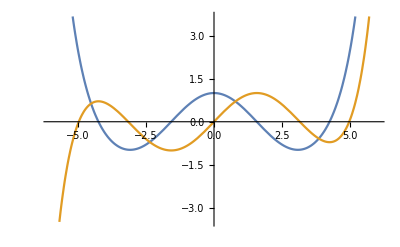

```mathematica
Plot[{1-x^2/2+x^4/24-x^6/720+x^8/40320,x-x^3/6+x^5/120-x^7/5040+x^9/362880},{x,-6,6}]
```

```mathematica
{Sin[x],D[Sin[x],x]}
```

{Sin[x],Cos[x]}

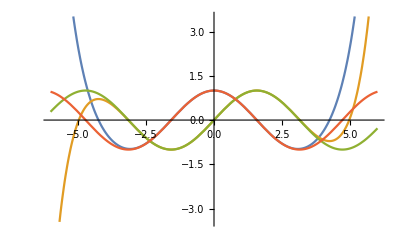

```mathematica
Plot[{1-x^2/2+x^4/24-x^6/720+x^8/40320,x-x^3/6+x^5/120-x^7/5040+x^9/362880,Sin[x],Cos[x]},{x,-6,6}]
```

```mathematica
FinancialData["NASDAQ:AAPL","Price", All][[;;10]]
```

Part::take: Cannot take positions 1 through 10 in ….

TimeSeries[…]⟦1;;10⟧

```mathematica
FinancialData["NASDAQ:AAPL","Price", All]["Values"][[;;10]]
```

QuantityArray[…]

```mathematica
Total[%14]
```

5.19 $

```mathematica
Differences@FinancialData["NASDAQ:AAPL","Price", All]["Values"][[;;10]]
```

{-0.03 $,-0.04 $,0.01 $,0.01 $,0.03 $,0.02 $,0.02 $,0.03 $,0.05 $}

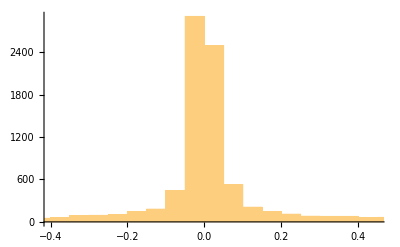

```mathematica
Histogram[Differences@FinancialData["NASDAQ:AAPL","Price", All]["Values"]]
```

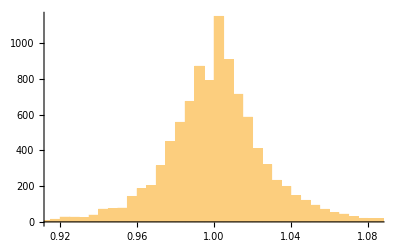

```mathematica
Histogram[Ratios@FinancialData["NASDAQ:AAPL","Price", All]["Values"]]
```

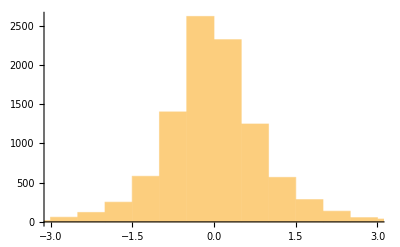

```mathematica
Histogram[Standardize@Ratios@FinancialData["NASDAQ:AAPL","Price", All]["Values"]]
```

```mathematica
apple=FinancialData["NASDAQ:AAPL","Price", All]["Values"]
```

QuantityArray[…]

```mathematica
Range@10
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Subsets@Range@5
```

{{},{1},{2},{3},{4},{5},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5},{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,4,5}}

```mathematica
Mean@Range@5
```

3

```mathematica
Range@5
```

{1,2,3,4,5}

```mathematica
Mean@Range@5
```

3

```mathematica
Subsets@Range@5
```

{{},{1},{2},{3},{4},{5},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5},{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,4,5}}

```mathematica
Map[Mean,Subsets@Range@5]
```

{Mean[{}],1,2,3,4,5,3/2,2,5/2,3,5/2,3,7/2,7/2,4,9/2,2,7/3,8/3,8/3,3,10/3,3,10/3,11/3,4,5/2,11/4,3,13/4,7/2,3}

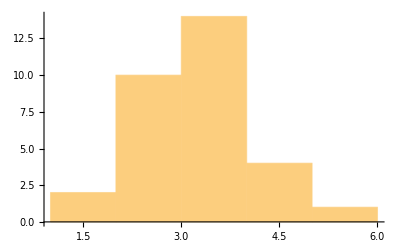

```mathematica
Histogram[{1,2,3,4,5,3/2,2,5/2,3,5/2,3,7/2,7/2,4,9/2,2,7/3,8/3,8/3,3,10/3,3,10/3,11/3,4,5/2,11/4,3,13/4,7/2,3}]
```

```mathematica
Mean[{1,2,3,4,5,3/2,2,5/2,3,5/2,3,7/2,7/2,4,9/2,2,7/3,8/3,8/3,3,10/3,3,10/3,11/3,4,5/2,11/4,3,13/4,7/2,3}]
```

3

```mathematica
Map[Mean,Subsets@Range@10]
```

{Mean[{}],1,2,3,4,5,6,7,8,9,10,3/2,2,5/2,3,7/2,4,9/2,5,11/2,5/2,3,7/2,4,9/2,5,11/2,6,7/2,4,9/2,5,11/2,6,13/2,9/2,5,11/2,6,13/2,7,11/2,6,13/2,7,15/2,13/2,7,15/2,8,15/2,8,17/2,17/2,9,19/2,2,7/3,8/3,3,10/3,11/3,4,13/3,8/3,3,10/3,11/3,4,13/3,14/3,10/3,11/3,4,13/3,14/3,5,4,13/3,14/3,5,16/3,14/3,5,16/3,17/3,16/3,17/3,6,6,19/3,20/3,3,10/3,11/3,4,13/3,14/3,5,11/3,4,13/3,14/3,5,16/3,13/3,14/3,5,16/3,17/3,5,16/3,17/3,6,17/3,6,19/3,19/3,20/3,7,4,13/3,14/3,5,16/3,17/3,14/3,5,16/3,17/3,6,16/3,17/3,6,19/3,6,19/3,20/3,20/3,7,22/3,5,16/3,17/3,6,19/3,17/3,6,19/3,20/3,19/3,20/3,7,7,22/3,23/3,6,19/3,20/3,7,20/3,7,22/3,22/3,23/3,8,7,22/3,23/3,23/3,8,25/3,8,25/3,26/3,9,5/2,11/4,3,13/4,7/2,15/4,4,3,13/4,7/2,15/4,4,17/4,7/2,15/4,4,17/4,9/2,4,17/4,9/2,19/4,9/2,19/4,5,5,21/4,11/2,13/4,7/2,15/4,4,17/4,9/2,15/4,4,17/4,9/2,19/4,17/4,9/2,19/4,5,19/4,5,21/4,21/4,11/2,23/4,4,17/4,9/2,19/4,5,9/2,19/4,5,21/4,5,21/4,11/2,11/2,23/4,6,19/4,5,21/4,11/2,21/4,11/2,23/4,23/4,6,25/4,11/2,23/4,6,6,25/4,13/2,25/4,13/2,27/4,7,7/2,15/4,4,17/4,9/2,19/4,4,17/4,9/2,19/4,5,9/2,19/4,5,21/4,5,21/4,11/2,11/2,23/4,6,17/4,9/2,19/4,5,21/4,19/4,5,21/4,11/2,21/4,11/2,23/4,23/4,6,25/4,5,21/4,11/2,23/4,11/2,23/4,6,6,25/4,13/2,23/4,6,25/4,25/4,13/2,27/4,13/2,27/4,7,29/4,9/2,19/4,5,21/4,11/2,5,21/4,11/2,23/4,11/2,23/4,6,6,25/4,13/2,21/4,11/2,23/4,6,23/4,6,25/4,25/4,13/2,27/4,6,25/4,13/2,13/2,27/4,7,27/4,7,29/4,15/2,11/2,23/4,6,25/4,6,25/4,13/2,13/2,27/4,7,25/4,13/2,27/4,27/4,7,29/4,7,29/4,15/2,31/4,13/2,27/4,7,7,29/4,15/2,29/4,15/2,31/4,8,15/2,31/4,8,33/4,17/2,3,16/5,17/5,18/5,19/5,4,17/5,18/5,19/5,4,21/5,19/5,4,21/5,22/5,21/5,22/5,23/5,23/5,24/5,5,18/5,19/5,4,21/5,22/5,4,21/5,22/5,23/5,22/5,23/5,24/5,24/5,5,26/5,21/5,22/5,23/5,24/5,23/5,24/5,5,5,26/5,27/5,24/5,5,26/5,26/5,27/5,28/5,27/5,28/5,29/5,6,19/5,4,21/5,22/5,23/5,21/5,22/5,23/5,24/5,23/5,24/5,5,5,26/5,27/5,22/5,23/5,24/5,5,24/5,5,26/5,26/5,27/5,28/5,5,26/5,27/5,27/5,28/5,29/5,28/5,29/5,6,31/5,23/5,24/5,5,26/5,5,26/5,27/5,27/5,28/5,29/5,26/5,27/5,28/5,28/5,29/5,6,29/5,6,31/5,32/5,27/5,28/5,29/5,29/5,6,31/5,6,31/5,32/5,33/5,31/5,32/5,33/5,34/5,7,4,21/5,22/5,23/5,24/5,22/5,23/5,24/5,5,24/5,5,26/5,26/5,27/5,28/5,23/5,24/5,5,26/5,5,26/5,27/5,27/5,28/5,29/5,26/5,27/5,28/5,28/5,29/5,6,29/5,6,31/5,32/5,24/5,5,26/5,27/5,26/5,27/5,28/5,28/5,29/5,6,27/5,28/5,29/5,29/5,6,31/5,6,31/5,32/5,33/5,28/5,29/5,6,6,31/5,32/5,31/5,32/5,33/5,34/5,32/5,33/5,34/5,7,36/5,5,26/5,27/5,28/5,27/5,28/5,29/5,29/5,6,31/5,28/5,29/5,6,6,31/5,32/5,31/5,32/5,33/5,34/5,29/5,6,31/5,31/5,32/5,33/5,32/5,33/5,34/5,7,33/5,34/5,7,36/5,37/5,6,31/5,32/5,32/5,33/5,34/5,33/5,34/5,7,36/5,34/5,7,36/5,37/5,38/5,7,36/5,37/5,38/5,39/5,8,7/2,11/3,23/6,4,25/6,23/6,4,25/6,13/3,25/6,13/3,9/2,9/2,14/3,29/6,4,25/6,13/3,9/2,13/3,9/2,14/3,14/3,29/6,5,9/2,14/3,29/6,29/6,5,31/6,5,31/6,16/3,11/2,25/6,13/3,9/2,14/3,9/2,14/3,29/6,29/6,5,31/6,14/3,29/6,5,5,31/6,16/3,31/6,16/3,11/2,17/3,29/6,5,31/6,31/6,16/3,11/2,16/3,11/2,17/3,35/6,11/2,17/3,35/6,6,37/6,13/3,9/2,14/3,29/6,14/3,29/6,5,5,31/6,16/3,29/6,5,31/6,31/6,16/3,11/2,16/3,11/2,17/3,35/6,5,31/6,16/3,16/3,11/2,17/3,11/2,17/3,35/6,6,17/3,35/6,6,37/6,19/3,31/6,16/3,11/2,11/2,17/3,35/6,17/3,35/6,6,37/6,35/6,6,37/6,19/3,13/2,6,37/6,19/3,13/2,20/3,41/6,9/2,14/3,29/6,5,29/6,5,31/6,31/6,16/3,11/2,5,31/6,16/3,16/3,11/2,17/3,11/2,17/3,35/6,6,31/6,16/3,11/2,11/2,17/3,35/6,17/3,35/6,6,37/6,35/6,6,37/6,19/3,13/2,16/3,11/2,17/3,17/3,35/6,6,35/6,6,37/6,19/3,6,37/6,19/3,13/2,20/3,37/6,19/3,13/2,20/3,41/6,7,11/2,17/3,35/6,35/6,6,37/6,6,37/6,19/3,13/2,37/6,19/3,13/2,20/3,41/6,19/3,13/2,20/3,41/6,7,43/6,13/2,20/3,41/6,7,43/6,22/3,15/2,4,29/7,30/7,31/7,30/7,31/7,32/7,32/7,33/7,34/7,31/7,32/7,33/7,33/7,34/7,5,34/7,5,36/7,37/7,32/7,33/7,34/7,34/7,5,36/7,5,36/7,37/7,38/7,36/7,37/7,38/7,39/7,40/7,33/7,34/7,5,5,36/7,37/7,36/7,37/7,38/7,39/7,37/7,38/7,39/7,40/7,41/7,38/7,39/7,40/7,41/7,6,43/7,34/7,5,36/7,36/7,37/7,38/7,37/7,38/7,39/7,40/7,38/7,39/7,40/7,41/7,6,39/7,40/7,41/7,6,43/7,44/7,40/7,41/7,6,43/7,44/7,45/7,46/7,5,36/7,37/7,37/7,38/7,39/7,38/7,39/7,40/7,41/7,39/7,40/7,41/7,6,43/7,40/7,41/7,6,43/7,44/7,45/7,41/7,6,43/7,44/7,45/7,46/7,47/7,6,43/7,44/7,45/7,46/7,47/7,48/7,7,9/2,37/8,19/4,19/4,39/8,5,39/8,5,41/8,21/4,5,41/8,21/4,43/8,11/2,41/8,21/4,43/8,11/2,45/8,23/4,21/4,43/8,11/2,45/8,23/4,47/8,6,43/8,11/2,45/8,23/4,47/8,6,49/8,25/4,11/2,45/8,23/4,47/8,6,49/8,25/4,51/8,13/2,5,46/9,47/9,16/3,49/9,50/9,17/3,52/9,53/9,6,11/2}

```mathematica
Mean@{1,2,3,4,5,6,7,8,9,10,3/2,2,5/2,3,7/2,4,9/2,5,11/2,5/2,3,7/2,4,9/2,5,11/2,6,7/2,4,9/2,5,11/2,6,13/2,9/2,5,11/2,6,13/2,7,11/2,6,13/2,7,15/2,13/2,7,15/2,8,15/2,8,17/2,17/2,9,19/2,2,7/3,8/3,3,10/3,11/3,4,13/3,8/3,3,10/3,11/3,4,13/3,14/3,10/3,11/3,4,13/3,14/3,5,4,13/3,14/3,5,16/3,14/3,5,16/3,17/3,16/3,17/3,6,6,19/3,20/3,3,10/3,11/3,4,13/3,14/3,5,11/3,4,13/3,14/3,5,16/3,13/3,14/3,5,16/3,17/3,5,16/3,17/3,6,17/3,6,19/3,19/3,20/3,7,4,13/3,14/3,5,16/3,17/3,14/3,5,16/3,17/3,6,16/3,17/3,6,19/3,6,19/3,20/3,20/3,7,22/3,5,16/3,17/3,6,19/3,17/3,6,19/3,20/3,19/3,20/3,7,7,22/3,23/3,6,19/3,20/3,7,20/3,7,22/3,22/3,23/3,8,7,22/3,23/3,23/3,8,25/3,8,25/3,26/3,9,5/2,11/4,3,13/4,7/2,15/4,4,3,13/4,7/2,15/4,4,17/4,7/2,15/4,4,17/4,9/2,4,17/4,9/2,19/4,9/2,19/4,5,5,21/4,11/2,13/4,7/2,15/4,4,17/4,9/2,15/4,4,17/4,9/2,19/4,17/4,9/2,19/4,5,19/4,5,21/4,21/4,11/2,23/4,4,17/4,9/2,19/4,5,9/2,19/4,5,21/4,5,21/4,11/2,11/2,23/4,6,19/4,5,21/4,11/2,21/4,11/2,23/4,23/4,6,25/4,11/2,23/4,6,6,25/4,13/2,25/4,13/2,27/4,7,7/2,15/4,4,17/4,9/2,19/4,4,17/4,9/2,19/4,5,9/2,19/4,5,21/4,5,21/4,11/2,11/2,23/4,6,17/4,9/2,19/4,5,21/4,19/4,5,21/4,11/2,21/4,11/2,23/4,23/4,6,25/4,5,21/4,11/2,23/4,11/2,23/4,6,6,25/4,13/2,23/4,6,25/4,25/4,13/2,27/4,13/2,27/4,7,29/4,9/2,19/4,5,21/4,11/2,5,21/4,11/2,23/4,11/2,23/4,6,6,25/4,13/2,21/4,11/2,23/4,6,23/4,6,25/4,25/4,13/2,27/4,6,25/4,13/2,13/2,27/4,7,27/4,7,29/4,15/2,11/2,23/4,6,25/4,6,25/4,13/2,13/2,27/4,7,25/4,13/2,27/4,27/4,7,29/4,7,29/4,15/2,31/4,13/2,27/4,7,7,29/4,15/2,29/4,15/2,31/4,8,15/2,31/4,8,33/4,17/2,3,16/5,17/5,18/5,19/5,4,17/5,18/5,19/5,4,21/5,19/5,4,21/5,22/5,21/5,22/5,23/5,23/5,24/5,5,18/5,19/5,4,21/5,22/5,4,21/5,22/5,23/5,22/5,23/5,24/5,24/5,5,26/5,21/5,22/5,23/5,24/5,23/5,24/5,5,5,26/5,27/5,24/5,5,26/5,26/5,27/5,28/5,27/5,28/5,29/5,6,19/5,4,21/5,22/5,23/5,21/5,22/5,23/5,24/5,23/5,24/5,5,5,26/5,27/5,22/5,23/5,24/5,5,24/5,5,26/5,26/5,27/5,28/5,5,26/5,27/5,27/5,28/5,29/5,28/5,29/5,6,31/5,23/5,24/5,5,26/5,5,26/5,27/5,27/5,28/5,29/5,26/5,27/5,28/5,28/5,29/5,6,29/5,6,31/5,32/5,27/5,28/5,29/5,29/5,6,31/5,6,31/5,32/5,33/5,31/5,32/5,33/5,34/5,7,4,21/5,22/5,23/5,24/5,22/5,23/5,24/5,5,24/5,5,26/5,26/5,27/5,28/5,23/5,24/5,5,26/5,5,26/5,27/5,27/5,28/5,29/5,26/5,27/5,28/5,28/5,29/5,6,29/5,6,31/5,32/5,24/5,5,26/5,27/5,26/5,27/5,28/5,28/5,29/5,6,27/5,28/5,29/5,29/5,6,31/5,6,31/5,32/5,33/5,28/5,29/5,6,6,31/5,32/5,31/5,32/5,33/5,34/5,32/5,33/5,34/5,7,36/5,5,26/5,27/5,28/5,27/5,28/5,29/5,29/5,6,31/5,28/5,29/5,6,6,31/5,32/5,31/5,32/5,33/5,34/5,29/5,6,31/5,31/5,32/5,33/5,32/5,33/5,34/5,7,33/5,34/5,7,36/5,37/5,6,31/5,32/5,32/5,33/5,34/5,33/5,34/5,7,36/5,34/5,7,36/5,37/5,38/5,7,36/5,37/5,38/5,39/5,8,7/2,11/3,23/6,4,25/6,23/6,4,25/6,13/3,25/6,13/3,9/2,9/2,14/3,29/6,4,25/6,13/3,9/2,13/3,9/2,14/3,14/3,29/6,5,9/2,14/3,29/6,29/6,5,31/6,5,31/6,16/3,11/2,25/6,13/3,9/2,14/3,9/2,14/3,29/6,29/6,5,31/6,14/3,29/6,5,5,31/6,16/3,31/6,16/3,11/2,17/3,29/6,5,31/6,31/6,16/3,11/2,16/3,11/2,17/3,35/6,11/2,17/3,35/6,6,37/6,13/3,9/2,14/3,29/6,14/3,29/6,5,5,31/6,16/3,29/6,5,31/6,31/6,16/3,11/2,16/3,11/2,17/3,35/6,5,31/6,16/3,16/3,11/2,17/3,11/2,17/3,35/6,6,17/3,35/6,6,37/6,19/3,31/6,16/3,11/2,11/2,17/3,35/6,17/3,35/6,6,37/6,35/6,6,37/6,19/3,13/2,6,37/6,19/3,13/2,20/3,41/6,9/2,14/3,29/6,5,29/6,5,31/6,31/6,16/3,11/2,5,31/6,16/3,16/3,11/2,17/3,11/2,17/3,35/6,6,31/6,16/3,11/2,11/2,17/3,35/6,17/3,35/6,6,37/6,35/6,6,37/6,19/3,13/2,16/3,11/2,17/3,17/3,35/6,6,35/6,6,37/6,19/3,6,37/6,19/3,13/2,20/3,37/6,19/3,13/2,20/3,41/6,7,11/2,17/3,35/6,35/6,6,37/6,6,37/6,19/3,13/2,37/6,19/3,13/2,20/3,41/6,19/3,13/2,20/3,41/6,7,43/6,13/2,20/3,41/6,7,43/6,22/3,15/2,4,29/7,30/7,31/7,30/7,31/7,32/7,32/7,33/7,34/7,31/7,32/7,33/7,33/7,34/7,5,34/7,5,36/7,37/7,32/7,33/7,34/7,34/7,5,36/7,5,36/7,37/7,38/7,36/7,37/7,38/7,39/7,40/7,33/7,34/7,5,5,36/7,37/7,36/7,37/7,38/7,39/7,37/7,38/7,39/7,40/7,41/7,38/7,39/7,40/7,41/7,6,43/7,34/7,5,36/7,36/7,37/7,38/7,37/7,38/7,39/7,40/7,38/7,39/7,40/7,41/7,6,39/7,40/7,41/7,6,43/7,44/7,40/7,41/7,6,43/7,44/7,45/7,46/7,5,36/7,37/7,37/7,38/7,39/7,38/7,39/7,40/7,41/7,39/7,40/7,41/7,6,43/7,40/7,41/7,6,43/7,44/7,45/7,41/7,6,43/7,44/7,45/7,46/7,47/7,6,43/7,44/7,45/7,46/7,47/7,48/7,7,9/2,37/8,19/4,19/4,39/8,5,39/8,5,41/8,21/4,5,41/8,21/4,43/8,11/2,41/8,21/4,43/8,11/2,45/8,23/4,21/4,43/8,11/2,45/8,23/4,47/8,6,43/8,11/2,45/8,23/4,47/8,6,49/8,25/4,11/2,45/8,23/4,47/8,6,49/8,25/4,51/8,13/2,5,46/9,47/9,16/3,49/9,50/9,17/3,52/9,53/9,6,11/2}
```

11/2

```mathematica
Mean@Range@10
```

11/2

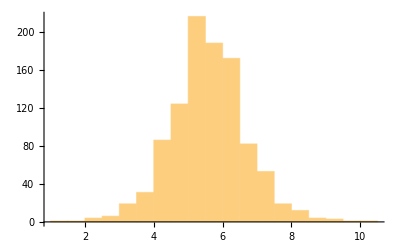

```mathematica
Histogram@{1,2,3,4,5,6,7,8,9,10,3/2,2,5/2,3,7/2,4,9/2,5,11/2,5/2,3,7/2,4,9/2,5,11/2,6,7/2,4,9/2,5,11/2,6,13/2,9/2,5,11/2,6,13/2,7,11/2,6,13/2,7,15/2,13/2,7,15/2,8,15/2,8,17/2,17/2,9,19/2,2,7/3,8/3,3,10/3,11/3,4,13/3,8/3,3,10/3,11/3,4,13/3,14/3,10/3,11/3,4,13/3,14/3,5,4,13/3,14/3,5,16/3,14/3,5,16/3,17/3,16/3,17/3,6,6,19/3,20/3,3,10/3,11/3,4,13/3,14/3,5,11/3,4,13/3,14/3,5,16/3,13/3,14/3,5,16/3,17/3,5,16/3,17/3,6,17/3,6,19/3,19/3,20/3,7,4,13/3,14/3,5,16/3,17/3,14/3,5,16/3,17/3,6,16/3,17/3,6,19/3,6,19/3,20/3,20/3,7,22/3,5,16/3,17/3,6,19/3,17/3,6,19/3,20/3,19/3,20/3,7,7,22/3,23/3,6,19/3,20/3,7,20/3,7,22/3,22/3,23/3,8,7,22/3,23/3,23/3,8,25/3,8,25/3,26/3,9,5/2,11/4,3,13/4,7/2,15/4,4,3,13/4,7/2,15/4,4,17/4,7/2,15/4,4,17/4,9/2,4,17/4,9/2,19/4,9/2,19/4,5,5,21/4,11/2,13/4,7/2,15/4,4,17/4,9/2,15/4,4,17/4,9/2,19/4,17/4,9/2,19/4,5,19/4,5,21/4,21/4,11/2,23/4,4,17/4,9/2,19/4,5,9/2,19/4,5,21/4,5,21/4,11/2,11/2,23/4,6,19/4,5,21/4,11/2,21/4,11/2,23/4,23/4,6,25/4,11/2,23/4,6,6,25/4,13/2,25/4,13/2,27/4,7,7/2,15/4,4,17/4,9/2,19/4,4,17/4,9/2,19/4,5,9/2,19/4,5,21/4,5,21/4,11/2,11/2,23/4,6,17/4,9/2,19/4,5,21/4,19/4,5,21/4,11/2,21/4,11/2,23/4,23/4,6,25/4,5,21/4,11/2,23/4,11/2,23/4,6,6,25/4,13/2,23/4,6,25/4,25/4,13/2,27/4,13/2,27/4,7,29/4,9/2,19/4,5,21/4,11/2,5,21/4,11/2,23/4,11/2,23/4,6,6,25/4,13/2,21/4,11/2,23/4,6,23/4,6,25/4,25/4,13/2,27/4,6,25/4,13/2,13/2,27/4,7,27/4,7,29/4,15/2,11/2,23/4,6,25/4,6,25/4,13/2,13/2,27/4,7,25/4,13/2,27/4,27/4,7,29/4,7,29/4,15/2,31/4,13/2,27/4,7,7,29/4,15/2,29/4,15/2,31/4,8,15/2,31/4,8,33/4,17/2,3,16/5,17/5,18/5,19/5,4,17/5,18/5,19/5,4,21/5,19/5,4,21/5,22/5,21/5,22/5,23/5,23/5,24/5,5,18/5,19/5,4,21/5,22/5,4,21/5,22/5,23/5,22/5,23/5,24/5,24/5,5,26/5,21/5,22/5,23/5,24/5,23/5,24/5,5,5,26/5,27/5,24/5,5,26/5,26/5,27/5,28/5,27/5,28/5,29/5,6,19/5,4,21/5,22/5,23/5,21/5,22/5,23/5,24/5,23/5,24/5,5,5,26/5,27/5,22/5,23/5,24/5,5,24/5,5,26/5,26/5,27/5,28/5,5,26/5,27/5,27/5,28/5,29/5,28/5,29/5,6,31/5,23/5,24/5,5,26/5,5,26/5,27/5,27/5,28/5,29/5,26/5,27/5,28/5,28/5,29/5,6,29/5,6,31/5,32/5,27/5,28/5,29/5,29/5,6,31/5,6,31/5,32/5,33/5,31/5,32/5,33/5,34/5,7,4,21/5,22/5,23/5,24/5,22/5,23/5,24/5,5,24/5,5,26/5,26/5,27/5,28/5,23/5,24/5,5,26/5,5,26/5,27/5,27/5,28/5,29/5,26/5,27/5,28/5,28/5,29/5,6,29/5,6,31/5,32/5,24/5,5,26/5,27/5,26/5,27/5,28/5,28/5,29/5,6,27/5,28/5,29/5,29/5,6,31/5,6,31/5,32/5,33/5,28/5,29/5,6,6,31/5,32/5,31/5,32/5,33/5,34/5,32/5,33/5,34/5,7,36/5,5,26/5,27/5,28/5,27/5,28/5,29/5,29/5,6,31/5,28/5,29/5,6,6,31/5,32/5,31/5,32/5,33/5,34/5,29/5,6,31/5,31/5,32/5,33/5,32/5,33/5,34/5,7,33/5,34/5,7,36/5,37/5,6,31/5,32/5,32/5,33/5,34/5,33/5,34/5,7,36/5,34/5,7,36/5,37/5,38/5,7,36/5,37/5,38/5,39/5,8,7/2,11/3,23/6,4,25/6,23/6,4,25/6,13/3,25/6,13/3,9/2,9/2,14/3,29/6,4,25/6,13/3,9/2,13/3,9/2,14/3,14/3,29/6,5,9/2,14/3,29/6,29/6,5,31/6,5,31/6,16/3,11/2,25/6,13/3,9/2,14/3,9/2,14/3,29/6,29/6,5,31/6,14/3,29/6,5,5,31/6,16/3,31/6,16/3,11/2,17/3,29/6,5,31/6,31/6,16/3,11/2,16/3,11/2,17/3,35/6,11/2,17/3,35/6,6,37/6,13/3,9/2,14/3,29/6,14/3,29/6,5,5,31/6,16/3,29/6,5,31/6,31/6,16/3,11/2,16/3,11/2,17/3,35/6,5,31/6,16/3,16/3,11/2,17/3,11/2,17/3,35/6,6,17/3,35/6,6,37/6,19/3,31/6,16/3,11/2,11/2,17/3,35/6,17/3,35/6,6,37/6,35/6,6,37/6,19/3,13/2,6,37/6,19/3,13/2,20/3,41/6,9/2,14/3,29/6,5,29/6,5,31/6,31/6,16/3,11/2,5,31/6,16/3,16/3,11/2,17/3,11/2,17/3,35/6,6,31/6,16/3,11/2,11/2,17/3,35/6,17/3,35/6,6,37/6,35/6,6,37/6,19/3,13/2,16/3,11/2,17/3,17/3,35/6,6,35/6,6,37/6,19/3,6,37/6,19/3,13/2,20/3,37/6,19/3,13/2,20/3,41/6,7,11/2,17/3,35/6,35/6,6,37/6,6,37/6,19/3,13/2,37/6,19/3,13/2,20/3,41/6,19/3,13/2,20/3,41/6,7,43/6,13/2,20/3,41/6,7,43/6,22/3,15/2,4,29/7,30/7,31/7,30/7,31/7,32/7,32/7,33/7,34/7,31/7,32/7,33/7,33/7,34/7,5,34/7,5,36/7,37/7,32/7,33/7,34/7,34/7,5,36/7,5,36/7,37/7,38/7,36/7,37/7,38/7,39/7,40/7,33/7,34/7,5,5,36/7,37/7,36/7,37/7,38/7,39/7,37/7,38/7,39/7,40/7,41/7,38/7,39/7,40/7,41/7,6,43/7,34/7,5,36/7,36/7,37/7,38/7,37/7,38/7,39/7,40/7,38/7,39/7,40/7,41/7,6,39/7,40/7,41/7,6,43/7,44/7,40/7,41/7,6,43/7,44/7,45/7,46/7,5,36/7,37/7,37/7,38/7,39/7,38/7,39/7,40/7,41/7,39/7,40/7,41/7,6,43/7,40/7,41/7,6,43/7,44/7,45/7,41/7,6,43/7,44/7,45/7,46/7,47/7,6,43/7,44/7,45/7,46/7,47/7,48/7,7,9/2,37/8,19/4,19/4,39/8,5,39/8,5,41/8,21/4,5,41/8,21/4,43/8,11/2,41/8,21/4,43/8,11/2,45/8,23/4,21/4,43/8,11/2,45/8,23/4,47/8,6,43/8,11/2,45/8,23/4,47/8,6,49/8,25/4,11/2,45/8,23/4,47/8,6,49/8,25/4,51/8,13/2,5,46/9,47/9,16/3,49/9,50/9,17/3,52/9,53/9,6,11/2}
```

```mathematica
Manipulate[
Histogram[Map[Mean,Subsets@Range@a][[;;-1]]]
,{a,1,20,1}]
```

```mathematica
Histogram[Differences@apple]
```

-Graphics-

```mathematica
Histogram[Ratios@apple]
```

-Graphics-

```mathematica
Quantity[24,"Hours"]/1000
```

3/125 h

```mathematica
UnitConvert[Quantity[3/125,"Hours"],MixedUnit[{"Minutes","Seconds"}]]
```

1 132/5